1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

22

23

24

25

26

27

28

29

30

31

32

33

34

35

36

37

38

39

40

41

42

43

44

45

46

47

48

49

50

51

52

53

54

55

56

57

58

59

60

61

62

63

64

65

66

67

68

69

70

71

72

73

74

75

76

77

78

79

80

81

82

83

84

85

86

87

88

89

90

91

92

93

94

95

96

97

98

99

100

{-2.00078,3.99944,-1.99494,1.99755,0.860805,0.600453,1.69553,1.41472}

Param | Est. | SE | True
γ_1 | -2.001 |  0.012 | -2.000
γ_2 |  3.999 |  0.027 |  4.000
β_π | -1.995 |  0.058 | -2.000
β_k |  1.998 |  0.063 |  2.000
δ |  0.861 |  0.249 |  0.900
ρ |  0.600 |  0.150 |  0.612
σ_ξ |  1.696 |  0.171 |  1.732
σ_η |  1.415 |  0.022 |  1.414

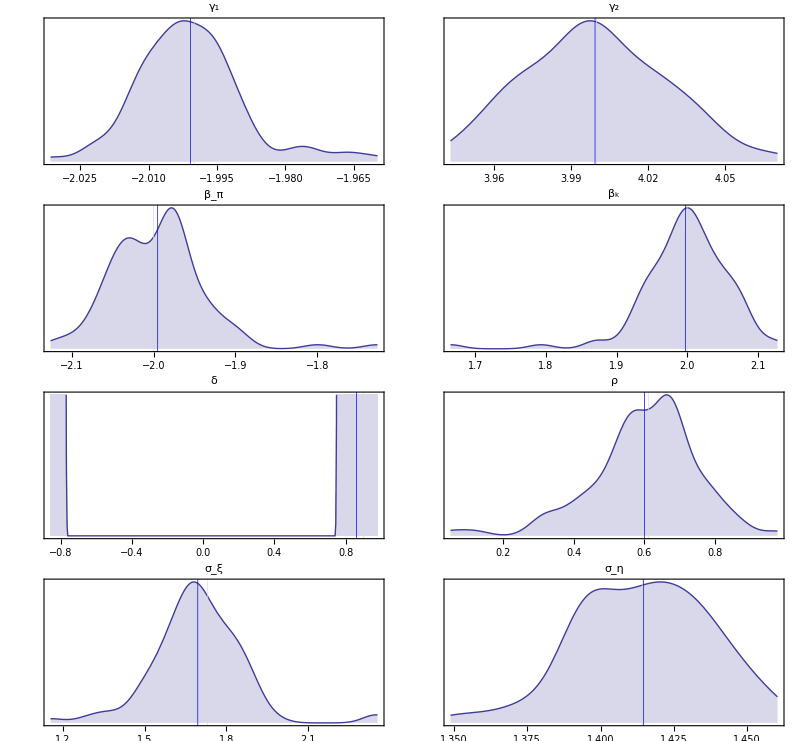
-Graphics-DensityValueN=1000, Draws=100

```mathematica
<<Ziena`
Clear["Global`*"]
SeedRandom[2]
BaseDir="C:\\Users\\Tim\\Dropbox\\Current Projects\\mathematica\\Tim\\dynamic_model";
CodeDir=BaseDir<>"\\code";
DataDir=BaseDir<>"\\data";
FigDir=BaseDir<>"\\figures";
OutputDir=BaseDir<>"\\output";
TableDir=BaseDir<>"\\tables";

(* sets the sample size *)
M=1000;

(* sets the parameters of the data distribution *)
pz=3;
mz=0;
pk=2;
mk=0;
pn=2;
mn=0;
py=2;
my=0;

(* sets the parameters of the error distribution *)
pϵ=2;
pη=2;
pϵη=.5;
mϵ=0;
mη=0;
stdxi=(pϵ+pη-2*pϵη)^.5;

(* sets the coefficients in choice equation *)
g1=-2;
g2=4;
Bk=2;
Bp=-2;
delta=.9;




(* draws the sample *)
k = RandomVariate[NormalDistribution[mk,pk],M];
z = RandomVariate[NormalDistribution[mz,pz],M];
n = RandomVariate[NormalDistribution[mn,pn],M];
y = RandomVariate[NormalDistribution[my,py],M];
h1=Table[0,{i,1,M,1}];
Φ[c_]:=CDF[NormalDistribution[0,1],c];
ϕ[c_]:=PDF[NormalDistribution[0,1],c];
(* draws the errors *)
eq1  = RandomVariate[MultinormalDistribution[{mϵ,mη},{{pη,pϵη},{pϵη,pη}}], M];
e1=eq1[[All,1]];
q1=eq1[[All,2]];

eq2  = RandomVariate[MultinormalDistribution[{mϵ,mη},{{pη,pϵη},{pϵη,pη}}], M];
e2=eq2[[All,1]];
q2=eq2[[All,2]];

eq3  = RandomVariate[MultinormalDistribution[{mϵ,mη},{{pη,pϵη},{pϵη,pη}}], M];
e3=eq3[[All,1]];
q3=eq3[[All,2]];

Put[e3,OutputDir"\\errors3"]

Export[Direct<>"\\estimates.dat",bootstrap,"Table"];
Export[Direct<>"\\truevalues.dat",truevalues,"Table"];
Export[Direct<>"\\meanvalues.dat",meanvalues,"Table"];
Export[Direct<>"\\counts.dat",counts];

(*,Algorithm->"Direct", Hessian->"Exact")
```